# Display of polyhedral Metal - Organic Cages

## Define Functions

Define a function that dictates style to display polyhedra: LINK
Generate video from 3D graphic: LINK
Add spheres to vertices: LINK

```mathematica
view[v_, f_, s_] := 
  Show[Graphics3D[{EdgeForm[{Thick}], 
  Polygon /@ Map[v[[#1]] & , f, {2}], Black, Sphere[v, s]}],
  PlotRange-> All,Boxed -> False]

hexToRGB = RGBColor @@ (IntegerDigits[# ~StringDrop~ 1 ~FromDigits~ 16, 256, 3]/255.) &;
```

Define a function to obtain faces from a graph: LINK

```mathematica
nextCandidate[s_, t_, adj_] :=
   Block[{ length, pos},
      length = Length[adj];
      pos = Mod[Position[adj, s][[1, 1]] + 1, length, 1];
      {t, adj[[pos]]}
    ];
    
FindFace[g_?PlanarGraphQ] :=
   Block[{emb},
      emb = GraphEmbedding[g, "PlanarEmbedding"];
      FindFace[g, emb]
   ];

FindFace[g_?PlanarGraphQ, emb_] :=
   Block[{m, orderings, pAdj, rightF, s, t, initial, face},
       m = AdjacencyMatrix[g];
       Table[pAdj[v] = 
           SortBy[Pick[VertexList[g], m[[v]], 1], 
           ArcTan @@ (emb[[v]] - emb[[#]]) &], {v, VertexList[g]}];
       rightF[_] := False;
       Reap[
         Table[
           If[! rightF[e],
             s = e[[1]];
             t = e[[2]];
             initial = s;
             face = {s};
             While[t =!= initial,
               rightF[UndirectedEdge[s, t]] = True;
               {s, t} = nextCandidate[s, t, pAdj[t]];
               face = Join[face, {s}];
             ];
             Sow[face];
           ],
         {e, EdgeList[g]}]][[2, 1]]
     ]
```

Obtain info from a dmccooey file: LINK
+1 for all vertice numbers in face-assignments as dmcooey starts from 0

```mathematica
getDMMCCOOEYpolyhedron = 
  Import["http://dmccooey.com/polyhedra/" <> # <> ".txt", "Lines"] &;

split =  If[Length[#] == 4, Drop[#, {2}], #] & @
  Map[DeleteCases["Faces:" | ""]] @
  Split[Drop[#, 2], ! StringStartsQ["Faces" | "V0" | "C0"] @ #2 &] &;

processStrings = Map @ 
  StringReplace[{"cbrt" -> "CubeRoot", "sqrt" -> "Sqrt", 
    "(" ~~ a__ ~~ ")" /; StringContainsQ[a, ","] :> "{" <> a <> "}",
    "=" ~~ a : Shortest[__] ~~ "=" ~~ __ :> "=" <> a}];

coordsAndFaceIndices = If[Length @ # == 2, {0, 1} + #,
  {#2, 1 + #3} & @@ #] & @ ToExpression[#, TraditionalForm] &;


fromDMCCCOOEY = coordsAndFaceIndices @* processStrings @* 
  split @* getDMMCCOOEYpolyhedron;
```

## Cuboctahedron

## Metal-Organic Cage (XRD Zn-1)

```mathematica
Zn1pdb = Import["/path-to-file/Zn-1.pdb", {"PDB", "Graphics3D"}]
```

-Graphics3D-

Draw polyhedron from xyz
1) Get vertices by extracting Zn-coordinates from xyz

```mathematica
Zn1 = Import["/path-to-file/Zn-1.xyz", "Table"];
metals = {"Mn", "Fe", "Co", "Ni", "Cu", "Zn", "Pd", "Pt", "Zr", "Na", "Mg"};
Corners = Select[Zn1, MemberQ[metals, First[#]] &];
vZn1 = Corners[[All, 2;;4]] // ToExpression
```

{{-4.86163,11.5559,0.317173},{5.16474,9.00766,8.05119},{-6.44873,3.97609,10.6751},{5.49756,-11.9878,0.814572},{-3.48525,-8.62559,9.52006},{8.32034,-3.41272,10.0108},{12.8537,2.82135,-0.38914},{4.1693,8.12969,-8.36669},{7.05235,-4.38181,-9.56941},{-12.1658,-3.20057,1.51393},{-4.61988,-9.45846,-6.94561},{-7.72176,2.92236,-8.93044}}

2) Obtain the vertex-connectivity in Scigress by deleting all atoms except Zn-vertices

```mathematica
Zn1Step2 = Import["/path-to-file/Zn-1_Connections.pdb", {"PDB", "Graphics3D"}]
```

-Graphics3D-

3) Do a MM3 optimization and save as pdb (#This is definitely not the most optimal way to do it)

```mathematica
Zn1Step3 = Import["/path-to-file/Zn-1_Connections2.pdb", {"PDB", "Graphics3D"}]
```

-Graphics3D-

4) Import pdb as molecule in mathematica: LINK

```mathematica
Zn2Step4 = Import["/path-to-file/Zn-1_Connections2.pdb", "Molecule"]
```

Molecule[…]

5) Creating a graph from pdb
	a) Create a molecular graph: LINK
	b) Obtain adjacency matrix
	c) Obtain planar graph
	d) Display nicer planar graph (still ugly though): LINK

```mathematica
Zn1Step5a = MoleculeGraph[Zn2Step4];
Zn1Step5b1 = AdjacencyMatrix[Zn1Step5a];
Zn1Step5b2 = AdjacencyMatrix[Zn1Step5a] // MatrixForm;
matrixImage = Rasterize[Zn1Step5b2, Background -> White];
Zn1Step5c = AdjacencyGraph[Zn1Step5b1, DirectedEdges -> False, GraphLayout -> "PlanarEmbedding", 
             VertexLabels -> "Name", ImagePadding -> 5];
                
Zn1Step5d = PlanarGraph[EdgeList[Zn1Step5c], VertexLabels -> "Name", PlotTheme -> "Classic"];
GraphicsRow[{Zn1Step5a, matrixImage, Zn1Step5c, Zn1Step5d}]
```

-Graphics-

6) Get face information from planar graph: LINK

{{1,2,7,8},{1,3,2},{1,8,12},{1,12,10,3},{2,3,5,6},{2,6,7},{3,10,5},{4,5,10,11},{4,6,5},{4,9,7,6},{4,11,9},{7,9,8},{8,9,11,12},{10,12,11}}

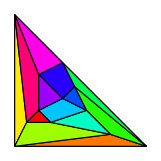

```mathematica
fZn1 = FindFace[Zn1Step5c]

CoordPlanarGraph = GraphEmbedding[Zn1Step5c];
colours = Table[Hue[x],{x,0,1,1/(Length[fZn1]-1)}];
colours2 = Table[RandomColor[],Length[fZn1]];
Graphics[{EdgeForm[Directive[Black, Thick]], 
 Thread[{colours [[;; Length[fZn1]]], 
           Polygon[CoordPlanarGraph[[#]]] & /@ fZn1}]}]
```

7) Display polyhedron

```mathematica
view[vZn1, fZn1, 0.8]
```

-Graphics3D-

8) Display without windows

```mathematica
fZn1windows = Select[fZn1, Length[#]!=3&];
fZn1triangles = Select[fZn1, Length[#]==3&]

fZn1trianglesblue = {{1,8,12}, {2,6,7}, {3,10,5},{ 4,11,9}}
fZn1trianglesgreen = {{1,3,2}, {4,6,5}, {7,9,8}, {10,12,11}}
  
 Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn1[[#1]] & , fZn1trianglesblue, {2}], hexToRGB["#EFA511"], Sphere[vZn1, 1]}], 
  Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#B0D094"]], 
  Polygon /@ Map[vZn1[[#1]] & , fZn1trianglesgreen, {2}], hexToRGB["#EFA511"], Sphere[vZn1, 1]}],
  PlotRange-> All, Boxed -> False]
  
Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn1[[#1]] & , {{1,3,2}}, {2}], hexToRGB["#E1CB6C"], Sphere[{{-4.861627,11.555873,0.317173},{5.164743,9.007659,8.051189},{-6.44873,3.97609,10.675092}}, 1]}],
  PlotRange-> All, Boxed -> False]
```

{{1,3,2},{1,8,12},{2,6,7},{3,10,5},{4,6,5},{4,11,9},{7,9,8},{10,12,11}}

{{1,8,12},{2,6,7},{3,10,5},{4,11,9}}

{{1,3,2},{4,6,5},{7,9,8},{10,12,11}}

-Graphics3D-

-Graphics3D-

## Pseudo-Johnson Solid 51

## Metal-Organic Cage Zn-2

```mathematica
Zn2pdb = Import["/path-to-file/Zn-2.pdb", {"PDB", "Graphics3D"}]
```

-Graphics3D-

1) Get vertices

```mathematica
Zn2 = Import["/path-to-file/Zn-2.xyz", "Table"];
metals = {"Mn", "Fe", "Co", "Ni", "Cu", "Zn", "Pd", "Pt", "Zr", "Na", "Mg"};
Corners = Select[Zn2, MemberQ[metals, First[#]] &];
vZn2 = Corners[[All, 2;;4]] // ToExpression
```

{{2.72324,-10.0443,7.64118},{-4.81529,-1.47068,11.1091},{-8.48463,-9.57685,3.15372},{0.688776,3.22695,-12.2325},{0.419369,11.9051,-3.96914},{10.2554,5.35386,-5.1961},{-7.05646,0.490834,-2.64328},{5.21181,3.59759,6.08421},{2.88285,-6.27068,-4.19677}}

2-6) Get faces

```mathematica
Zn2Step2 = Import["/path-to-file/Zn-2_Connections.pdb", {"PDB", "Graphics3D"}];
Zn2Step3 = Import["/path-to-file/Zn-2_Connections2.pdb", {"PDB", "Graphics3D"}]
Zn2Step4 = Import["/path-to-file/Zn-2_Connections2.pdb", "Molecule"];
Zn2Step5a = MoleculeGraph[Zn2Step4];
Zn2Step5b1 = AdjacencyMatrix[Zn2Step5a];
Zn2Step5b2 = AdjacencyMatrix[Zn2Step5a] // MatrixForm;
matrixImage = Rasterize[Zn2Step5b2, Background -> White];     
Zn2Step5c = AdjacencyGraph[Zn2Step5b1, DirectedEdges -> False, GraphLayout -> "PlanarEmbedding", 
             VertexLabels -> "Name", ImagePadding -> 5];         
Zn2Step5d = PlanarGraph[EdgeList[Zn2Step5c], VertexLabels -> "Name", PlotTheme -> "Classic"];
GraphicsRow[{Zn2Step5a, matrixImage, Zn2Step5c, Zn2Step5d}]
fZn2 = FindFace[Zn2Step5c]
```

-Graphics3D-

-Graphics-

{{1,2,8},{1,3,2},{1,8,6,9},{1,9,3},{2,3,7},{2,7,5,8},{3,9,4,7},{4,5,7},{4,6,5},{4,9,6},{5,6,8}}

7) Display MOC

```mathematica
fZn2windows = Select[fZn2, Length[#]!=3&];
fZn2triangles = Select[fZn2, Length[#]==3&];

vcyan = {-7.0564649,0.4908339,-2.64328};
vpurple = {{2.7232421,-10.0442881,7.641184},{-4.8152889,-1.4706801,11.109093},{-8.4846339,-9.5768501,3.153715}, {0.6887761,3.2269509,-12.232466},{0.4193691,11.9051459,-3.969138},{10.2553571,5.3538559,-5.196095}};

 Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn2[[#1]] & , fZn2triangles, {2}], hexToRGB["#EFA511"], Sphere[vZn2, 1]}], 
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#75FBFD"], Sphere[vcyan, 1]}],
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#AE317F"], Sphere[vpurple, 1]}],
  PlotRange-> All, Boxed -> False]
  
 Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn2[[#1]] & , fZn2triangles, {2}], hexToRGB["#EFA511"], Sphere[vZn2, 1]}], 
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#EFA511"], Sphere[vcyan, 1]}],
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#AE317F"], Sphere[vpurple, 1]}],
  PlotRange-> All, Boxed -> False]
  
 Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn2[[#1]] & , fZn2triangles, {2}], hexToRGB["#EFA511"], Sphere[vZn2, 1]}], 
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#EFA511"], Sphere[vcyan, 1]}],
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#EFA511"], Sphere[vpurple, 1]}],
  PlotRange-> All, Boxed -> False]
  
 Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn2[[#1]] & , fZn2triangles, {2}], hexToRGB["#75FBFD"], Sphere[vZn2, 1]}], 
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#EFA511"], Sphere[vcyan, 1]}],
  Graphics3D[{EdgeForm[{Thick}], hexToRGB["#AE317F"], Sphere[vpurple, 1]}],
  PlotRange-> All, Boxed -> False]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## Octahedron

## MOC Zn-3

```mathematica
Zn3pdb = Import["/path-to-file/Zn-3.pdb", {"PDB", "Graphics3D"}]
```

-Graphics3D-

1) Get vertices

```mathematica
Zn3 = Import["/path-to-file/Zn-3.xyz", "Table"];
metals = {"Mn", "Fe", "Co", "Ni", "Cu", "Zn", "Pd", "Pt", "Zr", "Na", "Mg"};
Corners = Select[Zn3, MemberQ[metals, First[#]] &];
vZn3 = Corners[[All, 2;;4]] // ToExpression
```

{{5.83295,16.8498,14.925},{6.90794,24.1937,24.5051},{0.924992,28.5537,14.925},{-5.97295,25.8127,24.5051},{-6.75694,18.4518,14.925},{-0.934992,13.8488,24.5051}}

2-6) Get faces

```mathematica
Zn3Step2 = Import["/path-to-file/Zn-3_Connections.pdb", {"PDB", "Graphics3D"}];
Zn3Step3 = Import["/path-to-file/Zn-3_Connections2.pdb", {"PDB", "Graphics3D"}]
Zn3Step4 = Import[/Users/paulateeuwen/Library/CloudStorage/OneDrive-UniversityofCambridge/PhD/Nitschke/Modelling/Mathematica/YuchongCages/Zn-3_Connections2.pdb", "Molecule"]
Zn3Step5a = MoleculeGraph[Zn3Step4];
Zn3Step5b1 = AdjacencyMatrix[Zn3Step5a];
Zn3Step5b2 = AdjacencyMatrix[Zn3Step5a] // MatrixForm;
Zn3Step5c = AdjacencyGraph[Zn3Step5b1, DirectedEdges -> False, GraphLayout -> "PlanarEmbedding", 
             VertexLabels -> "Name", ImagePadding -> 5];
                
Zn3Step5d = PlanarGraph[EdgeList[Zn3Step5c], VertexLabels -> "Name", PlotTheme -> "Classic"];
GraphicsRow[{Zn3Step5a, Zn3Step5b1, Zn3Step5c, Zn3Step5d}]
fZn3 = FindFace[Zn3Step5c]

view[vZn3, fZn3, 0.8]
```

-Graphics3D-

8) Obtain window-faces and display without windows

```mathematica
fZn3spanned = {{2,3,4},{1,2,6}, {5,6,4}, {5,3,1}}

Show[Graphics3D[{EdgeForm[{Thick}], FaceForm[hexToRGB["#9FAEE6"]], 
  Polygon /@ Map[vZn3[[#1]] & , fZn3spanned, {2}], hexToRGB["#D8EA1B"], Sphere[vZn3, 1]}], 
  PlotRange-> All, Boxed -> False]
```

{{2,3,4},{1,2,6},{5,6,4},{5,3,1}}

-Graphics3D-